## Initialisation

### fixed parameters

define ionisation potential, electric field amplitude  (intensity), fundamental wavelength...

```mathematica
Ip=0.5;
R = Tan[π/4];
ω = 0.057;
prefactor = ((ⅈ / Sqrt[π])*(2*Ip)^(1/4));
```

### Define fields

electric  field  definition, vector potential, derivative of the action, action, ...

```mathematica
(*Define the electric field function as a 2D vector*)
E1[t_]:={Cos[Pi/2] Cos[t]-Sin[Pi/2] Cos[2 t],0};
(*Define the vector potential components*)
Ax[tx_]:=-Integrate[E1[t][[1]],t]/. t->tx;
Ay[tx_]:=-Integrate[E1[t][[2]],t]/. t->tx;
(*Define the 2D vector potential A*)
A[tx_]:={Ax[tx],Ay[tx]};

(*Define Sf,Sfunc,DsFunc,D2sFunc,and action in terms of px,Ax,py,and Ay*)
Sf[tk_,p_List]=Integrate[2 (p[[1]]*Ax[t]+p[[2]]*Ay[t])+(Ax[t]^2+Ay[t]^2),t]/. t->tk;
(*Print[Sf[t,{px,py}]]*)
Sfunc[t_,p_List]:=0.5*Sf[t,p]+(0.5*(p[[1]]^2+p[[2]]^2)+Ip)*t;
(*Print[Sfunc[t,{px,py}]]*)
DsFunc[t_,p_List]:=D[Sfunc[tc,p],tc]/. tc->t;
(*Print[DsFunc[t,{px,py}]]*)
D2sFunc[t_,p_List]:=ω*D[Sfunc[tz,p],{tz,2}]/. tz->t;
(*Print[D2sFunc[t,{px,py}]]*)
action[t_,p_List]:=Exp[I*Sfunc[t,p]/ω];
(*Print[action[t,{px,py}]]*)
```

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

### Define the momentum grid

```mathematica
(*Define the range for px and py values*)
pxValues=Range[-1.9,1.9,0.1];
pyValues=Range[-1.9,1.9,0.1];
Print[Length[pxValues]]
Print[Length[pyValues]]
```

39

39

### Define plotting functions

```mathematica
(*Plot Ex and Ey and roots*)
plotEx:=Quiet[Plot[E1[t][[1]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]]

plotEy:=Quiet[Plot[E1[t][[2]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ey"},ImageSize->Large]];

plotRoots[filteredTValues_]:=Quiet[ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]];
```

SetDelayed::write: Tag Graphics in ()[filteredTValues_] is Protected.

### Create Grid of Seeds

```mathematica
(*Generate the grid of seeds*) 

(*pick realmin to realmax as the range to capture the 4 saddle points in a periodic range of 2Pi*)
realMin=-2.133;realMax=4.150;
imagMin=0;imagMax=3;
realSteps=10;imagSteps=10;

listofseeds=Flatten[Table[x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];

(*Add the specific initial guess to the list of seeds*)
initialGuess=-2.0334+1.2321 ⅈ;
listofseeds=Prepend[listofseeds,initialGuess];

(*Ensure seeds are numerical values*)
listofseeds=N[listofseeds];

(*Extract real and imaginary parts of the seeds*)
seedPoints={Re[#],Im[#]}&/@listofseeds;
```

Find  all  the  roots for all px and py values (saddle point solutions)

```mathematica
ClearAll[generatePlotAndRoots];

(*Function to generate plots and roots for given px and py*)
generatePlotAndRoots[px_,py_,seeds_]:=
Module[
{allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues},
(*Find roots*)
allSolutions=Round[t/. Quiet[Table[FindRoot[DsFunc[t,{px,py}]==0,{t,tseed}],{tseed,seeds}]],0.0001];
complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];
(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#,{px,py}]]]<=tolerance&&Abs[Im[DsFunc[#,{px,py}]]]<=tolerance&];
{filteredTValues}];
```

## CALCULATION : Saddle Point Solutions

```mathematica
Calculate all the time saddle point solutions value for corresponding px and py below
```

```mathematica
(*Generate results using the precise px and py values*)
results=
(*ParallelTable works similarly to Table,but it distributes the computation across multiple CPU cores,allowing for parallel execution and significantly speeding up the process.*)
ParallelTable[
generatePlotAndRoots[px,py,listofseeds],
{px,pxValues}, {py,pyValues}
]
```

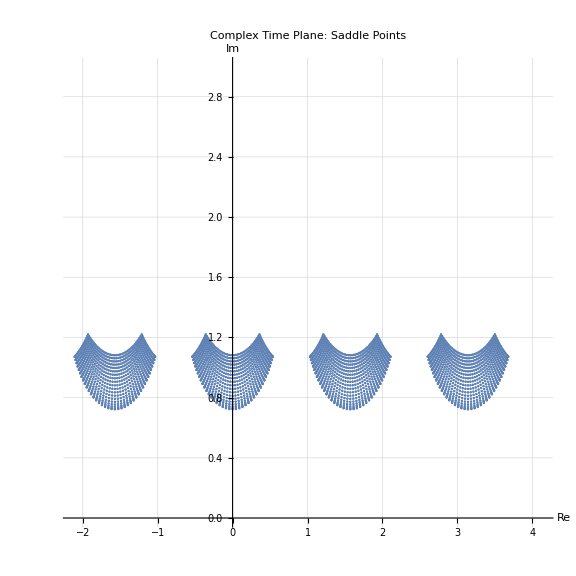

```mathematica
(*Flatten the nested array*)
flatResults=Flatten[results];

(*Extract real and imaginary parts*)
extraction=Map[{Re[#],Im[#]}&,flatResults];

(*Plot the time saddle points*)
ListPlot[{extraction},AxesLabel->{"Re","Im"},PlotRange->{{realMin,realMax},{imagMin,imagMax}},AspectRatio->1,GridLines->Automatic,PlotLabel->"Complex Time Plane: Saddle Points", ImageSize->Large]
```

## rearrange data structure of the time arrays & prep them for plotting.

```mathematica
newResults=
Table[{
(*Calculate pxValue based on the index i*)
pxValue=-1.9+(i-1)*0.1,
(*Calculate pyValue based on the index j*)
pyValue=-1.9+(j-1)*0.1,
(*Extract the corresponding results for the current px and py values*)
results[[i,j]]},
(*Iterate over the length of the results list for both i and j*)
{i,Length[results]},{j,Length[results]}
];

(*Get the number of elements in each sub-array at the forth level*)
forthLevelCounts=Length/@#&/@#&/@#&/@newResults;
(*Print[forthLevelCounts];*)

(*Use Table to iterate over the nested arrays*)
Table[
Module[(*Use Module to create local variables px,py,and number*)
{px,py,number},
(*Assign the values of px,py,and number from the innerArray*)
{px,py,number}=innerArray;
(*Check if the first element of number is not equal to 4*)
If[First[number]=!=4,
Print["px: ",px,", py: ",py,", number: ",First[number]]
]
],
(*Iterate over each outerArray in forthLevelCounts*)
{outerArray,forthLevelCounts},
(*Iterate over each innerArray in the current outerArray*)
{innerArray,outerArray}];


(*Flatten the newResults list by one level to get a list of sublists, Map over each sublist in flattenedResults For each sublist elem,join the first two elements with the elements of the nested list inside the third element.*)
tsExtended=Map[Function[{elem},Join[{elem[[1]],elem[[2]]},elem[[3,1]]]],Flatten[newResults,1]];
(*so essentially grabbing px and py and putting them in the same array as the time saddle point solutions ts1,ts2,ts3,ts4 so the array of arrays will look like {{px,py,ts1,ts2,ts3,ts4},repeat for different values of px and py}*)

(*-validData is a list of lists where each sublist contains four elements {Real part of ts,Imaginary part of ts,px,py}.*)
validData=
(*Select elements from the list that satisfy a condition*)
Select[
(*Flatten the nested list into a single list*)
Flatten[
(*Generate a table of values*)
Table[
(*Conditional statement to check if the element is not Null*)
If[tsExtended[[i,j+2]]=!=Null,
{(*Real part of the complex number*)
Re[tsExtended[[i,j+2]]],
(*Imaginary part of the complex number*)
Im[tsExtended[[i,j+2]]],
(*px value*)
tsExtended[[i,1]],
(*py value*)
tsExtended[[i,2]]},
(*If the element is Null,return Nothing*)
Nothing],
(*Iterate over all rows of tsExtended*)
{i,Length[tsExtended]},
(*Iterate over all columns except the first two*)
{j,1,Length[tsExtended[[i]]]-2}],
(*-Flatten at level 1 converts the nested list into a single list*)
1],
(*-Select filters the flattened list to include only the elements where the first element is not Null*)
#[[1]]=!=Null&]

(*length of valid data should be equal to the check solutions variable, if not there are missing saddle points as every saddle point px and py should have 4 saddle points*)
checksolutions = Length[pxValues]*Length[pyValues]*4;
Print[checksolutions];
Print[Length[validData]];
x=checksolutions-Length[validData];
Print["how many saddle point solutions are we missing: ",x]

(*Extract real and imaginary times from validData*)
realAndImagTimes=validData[[All,1;;2]];
(*[[All,1;;2]] is a part specification that extracts specific elements from each sublist. All indicates that we want to apply the extraction to all sublists in validData.   
1;;2 specifies the range of elements to extract from each sublist. In this case it extracts the first and second element [the real and imaginary parts of the saddle point solutions]*)

(*Generate a 2D heatmap for px and py using the Rainbow color scheme*)
colorFunction[pxOrPy_]:=ColorData["Rainbow"][Rescale[pxOrPy,{-2,2}]];
(*Generate a list of colored points with the custom color function for px*)
coloredPointsPx=Table[{colorFunction[validData[[i,3]]],Point[validData[[i,1;;2]]]},{i,1,Length[validData]}];
(*Generate a list of colored points with the custom color function for py*)
coloredPointsPy=Table[{colorFunction[validData[[i,4]]],Disk[validData[[i,1;;2]],0.05]},{i,1,Length[validData]}];
(*Define a color function using the Rainbow color scheme*)
colorFunction[pxOrPy_]:=ColorData["Rainbow"][Rescale[pxOrPy,{-2,2}]];

(*Explanation:
-colorFunction is a function that takes a value (px or py) and maps it to a color.
-ColorData["Rainbow"] returns a function that generates colors from the Rainbow color scheme.
-Rescale[pxOrPy,{-2,2}] rescales the input value pxOrPy from the range {-2,2} to the range {0,1},which is required by ColorData.*)

(*Generate a list of colored points with the custom color function for px*)
coloredPointsPx=Table[{colorFunction[validData[[i,3]]],Point[validData[[i,1;;2]]]},{i,1,Length[validData]}];

(*Explanation:
-Table is used to generate a list of colored points.
-{i,1,Length[validData]} iterates over all elements in validData.
-colorFunction[validData[[i,3]]] applies the color function to the px value (third element) of the i_th sublist in validData.
-Point[validData[[i,1;;2]]] creates a point at the coordinates specified by the real and imaginary parts (first and second elements) of the i-th sublist in validData.
-The result is a list of pairs,where each pair consists of a color and a point.*)

(*Generate a list of colored points with the custom color function for py*)
coloredPointsPy=Table[{colorFunction[validData[[i,4]]],Disk[validData[[i,1;;2]],0.05]},{i,1,Length[validData]}];

(*Explanation:
-Table is used to generate a list of colored points.
-{i,1,Length[validData]} iterates over all elements in validData.
-colorFunction[validData[[i,4]]] applies the color function to the py value (fourth element) of the i_th sublist in validData.
-Disk[validData[[i,1;;2]],0.05] creates a disk at the coordinates specified by the real and imaginary parts (first and second elements) of the i_th sublist in validData,with a radius of 0.05.
-The result is a list of pairs,where each pair consists of a color and a disk.*)
```

6084

6084

how many saddle point solutions are we missing: 0

## Plotting Electric Field with Saddle Points Solutions + Complex Plane Time Saddle Points Plot

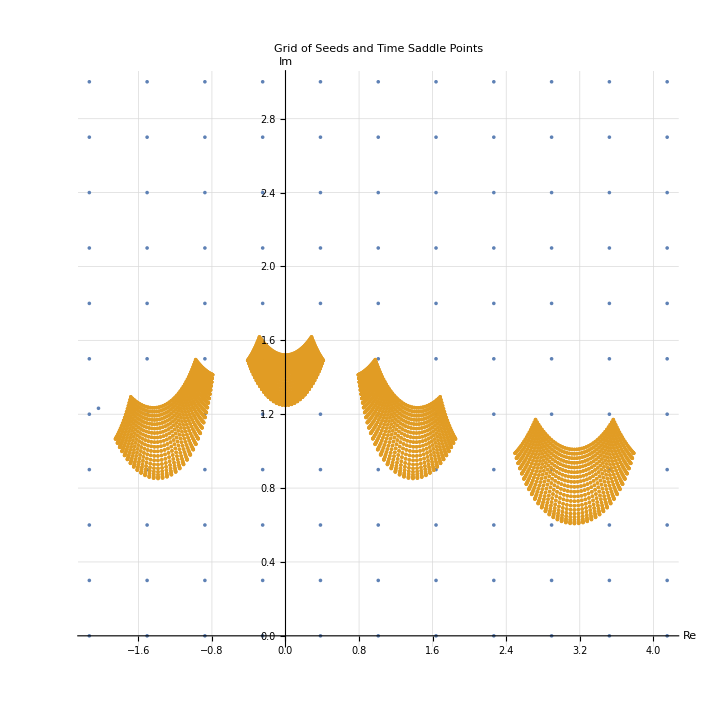

-Graphics3D-

```mathematica
Manipulate[
plotData=generatePlotAndRoots[px,py, listofseeds];
filteredTValues=plotData[[1]];
plotRoots=ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large];

Show[plotEx,plotEy,plotRoots,PlotRange->All,PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py]],{{px,0,"Momentum px"},-3,3,0.1},{{py,0,"Momentum py"},-3,3,0.1}]

Manipulate[
plotData=generatePlotAndRoots[px,py, listofseeds];
filteredTValues=plotData[[1]];
(*Extract time,Ex,and Ey values*)
timeValues=Re[#]&/@filteredTValues;
exValues=E1[#][[1]]&/@timeValues;
eyValues=E1[#][[2]]&/@timeValues;
(*Create root points for plotting*)
rootPoints=Graphics3D[{Red,PointSize[Large],Point[Transpose[{exValues,eyValues,timeValues}]]}];
(*Create 3D plot*)
Show[
ParametricPlot3D[{E1[t][[1]],E1[t][[2]],t},{t,-2.133,4.15},
PlotStyle->{Blue},AxesLabel->{"Electric Field Ex","Electric Field Ey","Time, t"},PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py]<>", 3D Electric Field Plot",ImageSize->{1200,600},PlotRange->All],
rootPoints,ImageSize->{1200,600}],{{px,0,"Momentum px"},-3,3,0.1},{{py,0,"Momentum py"},-3,3,0.1}]

(*Plot the grid of seeds and the time saddle points*)
ListPlot[{seedPoints,realAndImagTimes},AxesLabel->{"Re","Im"},PlotRange->{{realMin,realMax},{imagMin,imagMax}},AspectRatio->1,GridLines->Automatic,PlotLabel->"Grid of Seeds and Time Saddle Points"]

(*Plot the 3D graph with color representing py*)ListPointPlot3D[{#[[1]],#[[2]],#[[3]]}&/@validData,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","px"},PlotLabel->"4D Data Representation",ImageSize->Large,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Top}]]
```

# Calculating the Yield

if  the  saddle  point  solutions  generated  by  a  px  py  value  does  not  give  4  solutions  then  indexing  below  does  not  work  properly  as  it  assumes  format  of  time  saddle  points  to  be  ((px, py, ts1, ts2, ts3, ts4), so  on)  for  all  different  combinations  of  different  px  and  py  values .

```mathematica
(*Selects time saddle point solutions for trajectory A,B,C,D individually and accordingly*)
validData
timeA=Table[validData[[i]],{i,1,Length[validData],4}]
timeB=Table[validData[[i]],{i,2,Length[validData],4}];
timeC=Table[validData[[i]],{i,3,Length[validData],4}];
timeD=Table[validData[[i]],{i,4,Length[validData],4}];
Print[Length[timeA]]

(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A*)
psiA =Table[
prefactor*action[
timeA[[i,1]]+ⅈ*timeA[[i,2]],{timeA[[i,3]],timeA[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeA[[i,1]]+ⅈ*timeA[[i,2]],{timeA[[i,3]],timeA[[i,4]]}])
],
{i,1,Length[timeA]}];
Print[Length[psiA]]
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj B*)
psiB=Table[
prefactor*action[
timeB[[i,1]]+ⅈ*timeB[[i,2]],{timeB[[i,3]],timeB[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeB[[i,1]]+ⅈ*timeB[[i,2]],{timeB[[i,3]],timeB[[i,4]]}])
],
{i,1,Length[timeB]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiC=Table[
prefactor*action[
timeC[[i,1]]+ⅈ*timeC[[i,2]],{timeC[[i,3]],timeC[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeC[[i,1]]+ⅈ*timeC[[i,2]],{timeC[[i,3]],timeC[[i,4]]}])
],
{i,1,Length[timeC]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiD=Table[
prefactor*action[
timeD[[i,1]]+ⅈ*timeD[[i,2]],{timeD[[i,3]],timeD[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeD[[i,1]]+ⅈ*timeD[[i,2]],{timeD[[i,3]],timeD[[i,4]]}])
],
{i,1,Length[timeD]}];

(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A+B+C+D*)
totalPsi =psiA+psiB +psiC +psiD;
```

3391

3391

Thread::tdlen: Objects of unequal length in {-2.31687×10^-54-2.86077×10^-54 ⅈ,1.31968×10^-86+1.33077×10^-87 ⅈ,5.69376×10^-50+1.37649×10^-47 ⅈ,2.13114×10^-54+7.5167×10^-55 ⅈ,-1.92708×10^-42+6.82157×10^-42 ⅈ,-9.15479×10^-39+1.29593×10^-38 ⅈ,-3.80964×10^-67+5.12895×10^-67 ⅈ,3.06585×10^-108-1.21502×10^-107 ⅈ,6.74299×10^-107-5.93106×10^-106 ⅈ,-7.17307×10^-44-3.29549×10^-44 ⅈ,«3381»}+{-«23»-«23» ⅈ,«9»,«3381»}+«1»+{-6.40436×10^-52-3.20665×10^-52 ⅈ,9.66437×10^-59+5.30744×10^-58 ⅈ,«8»,«3380»} cannot be combined.

# Plotting The Yield

if the saddle point solutions generated by a px py value does not give 4 solutions then indexing below does not work properly as it assumes format of time saddle points to be ((px,py,ts1,ts2,ts3,ts4), so on) for all different combinations of different px and py values.

```mathematica
(*Create data points for each psi*)
dataA=Table[{pxValues[[i]],pyValues[[j]],Abs[psiA[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataB=Table[{pxValues[[i]],pyValues[[j]],Abs[psiB[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataC=Table[{pxValues[[i]],pyValues[[j]],Abs[psiC[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataD=Table[{pxValues[[i]],pyValues[[j]],Abs[psiD[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataTotal=Table[{pxValues[[i]],pyValues[[j]],Abs[totalPsi[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];

(*Flatten the data points*)
dataA=Flatten[dataA,1];
dataB=Flatten[dataB,1];
dataC=Flatten[dataC,1];
dataD=Flatten[dataD,1];
dataTotal=Flatten[dataTotal,1];

(*Create 3D plots for each psi Listlineplot*)
ListLinePlot3D[{dataA,dataB,dataC,dataD,dataTotal},PlotStyle->{Red,Green,Blue,Orange,Black},AxesLabel->{"px","py","Magnitude of the spectral ionisation amplitude |ΨSPM|"},SphericalRegion->True,ScalingFunctions->{None,None,"Log"},ImageSize->Full]

(*Create 3D plots for each psi Listplot*)
ListPlot3D[{dataA,dataB,dataC,dataD,dataTotal},PlotStyle->{Red,Green,Blue,Orange,Black},AxesLabel->{"px","py","Magnitude of the spectral ionisation amplitude |ΨSPM|"},SphericalRegion->True,ScalingFunctions->{None,None,"Log"},ImageSize->Full]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»